```mathematica
(* This is necessary for removing previously defined variables *)
ClearAll["Global`*"]
```

## Misc Modules

```mathematica
eps = 10^-6;
```

```mathematica
cosExpansion[x_]:=1-x^2/2+x^4/24-x^6/720;
```

```mathematica
stripList[lst_]:=Module[{lst2},
lst2 = List[];
Do[AppendTo[lst2,Last[lst[[ii]]]],{ii,Length[lst]}];
Return[lst2]]
```

```mathematica
a=List[{1},{2},{3}]
stripList[a]
```

```mathematica
(* Write Module to Count number of roots in a function *)
(* From https://www.physicsforums.com/threads/find-all-roots-of-an-interpolating-function-in-mathematica.612362/ *)
countZeros[ifun_,xmin_,xmax_,dx_] := Module[{zeros,numZeros},
zeros = Union[Table[x/.FindRoot[ifun[x]==0.,{x,xInit,xmin,xmax}],{xInit,xmin+dx,xmax-dx,dx}],SameTest->(Abs[#1-#2]<10^-4&)];
numZeros = Length[zeros];
Print[zeros];
If[Last[zeros]==xmax,If[ifun[xmax]≠0,numZeros=numZeros-1]];
If[First[zeros]==xmin,If[ifun[xmin]≠0,numZeros=numZeros-1]];
Return[numZeros]]
```

```mathematica
f[x_]:=x^4-x^2
countZeros[f,-2,2,0.1]
```

```mathematica
countAllZeros[ifun_,xmin_,xmax_,dx_,hardLim_]:=Module[{z,ztot,num,ii},
z=countZeros[ifun,xmin,xmax,dx];
Print["number of zeros for the function is ",z];
ztot=z;
If[z==0,num=0,num=1];
ii=1;
While[True,
f[x_]=D[ifun[x],{x,ii}];
If[f[x_]==0,Break[]];
z=countZeros[f,xmin,xmax,dx];
Print["number of zeros for ",ii,"th derivative is ",z];
ztot=ztot+z;
If[z==0,num++];
If[num≥2,Break[]];
If[ii≥hardLim,Break[]];
ii++];
Return[ztot]]
```

```mathematica
f[x_]:=x^4-x^2
countAllZeros[f,-10,10,0.1,1]
```

## Cosmology Calculation Modules

```mathematica
findZϵsr[v_,vp_,ϕsol_,nmin_,nmax_,dn_,hardLim_]:=Module[{ϵsr,f,z,num,ii,ztot},
ϵsr[x_]:=1/2*(vp[x]/v[x])^2;
f[n_]:=ϵsr[ϕ[n]]/.ϕsol;
Print[Plot[Evaluate[f[n]],{n,nmin,nmax},AxesLabel->{N,"ϵsr"},PlotRange->{-1,1}]];
z=countZeros[f,nmin,nmax,dn];
Print["number of zeros for ϵsr is ",z];
ztot=z;
If[z==0,num=0,num=1];
ii=1;
While[True,
f[n_]=D[ϵsr[ϕ[n]]/.ϕsol,{n,ii}];
Print[Plot[Evaluate[f[n]],{n,nmin,nmax},AxesLabel->{N,ii},PlotRange->{-1,1}]];
If[f[n_]==0,Break[]];
z=countZeros[f,nmin,nmax,dn];
Print["number of zeros for ",ii,"th derivative of ϵ is ",z];
ztot=ztot+z;
If[z==0,num++];
If[num≥2,Break[]];
If[ii≥hardLim,Break[]];
ii++];
Return[ztot]]
```

```mathematica
findZϵ[v_,ϕsol_,nmin_,nmax_,dn_,hardLim_]:=Module[{hsq,ϵ,f,z,num,ii,ztot},
hsq[n_]:=v[ϕ[n]]/(3-1/2*ϕ'[n]^2);
ϵ[n_] = Evaluate[3*ϕ'[n]^2/(ϕ'[n]^2+2*v[ϕ[n]]/hsq[n])];
f[n_] = ϵ[n]/.ϕsol;
Print[Plot[Evaluate[f[n]],{n,nmin,nmax},AxesLabel->{N,"ϵ"},PlotRange->{-1,1}]];
z=countZeros[f,nmin,nmax,dn];
Print["number of zeros for ϵ is ",z];
ztot=z;
If[z==0,num=0,num=1];
ii=1;
While[True,
f[n_]=D[ϵ[ϕ[n]],{n,ii}]/.ϕsol;
Print[Plot[Evaluate[f[n]],{n,nmin,nmax},AxesLabel->{N,ii},PlotRange->{-1,1}]];
If[f[n_]==0,Break[]];
z=countZeros[f,nmin,nmax,dn];
Print["number of zeros for ",ii,"th derivative of ϵ is ",z];
ztot=ztot+z;
If[z==0,num++];
If[num≥2,Break[]];
If[ii≥hardLim,Break[]];
ii++];
Return[ztot]]
```

```mathematica
findZη[v_,vpp_,ϕsol_,nmin_,nmax_,dn_,hardLim_]:=Module[{ηsr,f,z,num,ii,ztot},
ηsr[n_]:=vpp[ϕ[n]]/v[ϕ[n]];
f[n_]:=ηsr[ϕ[n]]/.ϕsol;
Print[Plot[Evaluate[f[n]],{n,nmin,nmax},AxesLabel->{N,"ηsr"},PlotRange->{-1,1}]];
z=countZeros[f,nmin,nmax,dn];
Print["number of zeros for ηsr is ",z];
ztot=z;
If[z==0,num=0,num=1];
ii=1;
While[True,
f[n_]=D[ηsr[ϕ[n]]/.ϕsol,{n,ii}];
Print[Plot[Evaluate[f[n]],{n,nmin,nmax},AxesLabel->{N,ii},PlotRange->{-1,1}]];
If[f[n_]==0,Break[]];
z=countZeros[f,nmin,nmax,dn];
Print["number of zeros for ",ii,"th derivative of η is ",z];
ztot=ztot+z;
If[z==0,num++];
If[num≥2,Break[]];
If[ii≥hardLim,Break[]];
ii++];
Return[ztot]]
```

```mathematica
findH[v_]:=Module[{h,hsq},
h[n_]:= Simplify[√(v[ϕ[n]]/(3-1/2*ϕ'[n]^2))];
hsq[n_]:=v[ϕ[n]]/(3-1/2*ϕ'[n]^2);
Return[{h,hsq}]]
```

### Find Initial Conditions for 1st Integration

```mathematica
chooseϕ0Manual[ϕ0list_]:=Module[{ϕ0index,ϕ0},
ϕ0index = Input["Enter the index for the ϕ0 you want to use: \n(Counting starts at 1)"];
ϕ0 = ϕ0list[[ϕ0index]]; 
Return[ϕ0]]
```

```mathematica
chooseϕ0Left[ϕ0list_,v_]:=Module[{ϕ0listpos,ϕ0,vacuumArray},
ϕ0listpos=Select[ϕ0list,#>0&];
(* vacuum = First[Select[ϕ0listpos,v[#]<10^-6&]];
ϕ0 = Max[Select[ϕ0listpos,#<vacuum&]]; *)
If[ϕ0listpos=={},
vacuumArray =Select[ϕ0list,v[#]<10^-6&];
Print["vacuumArray = ",vacuumArray];
If[vacuumArray=={},ϕ0=Min[ϕ0list],
ϕ0 = Min[Select[ϕ0list,#<First[vacuumArray]&]]];,
(*else*)
vacuumArray =Select[ϕ0listpos,v[#]<10^-6&];
Print["vacuumArray = ",vacuumArray];
If[vacuumArray=={},ϕ0=Min[ϕ0listpos],
ϕ0 = Max[Select[ϕ0listpos,#<First[vacuumArray]&]]];
];
Return[ϕ0]]
```

```mathematica
chooseϕ0Right[ϕ0list_,v_]:=Module[{ϕ0listpos,ϕ0,vacuumArray},
ϕ0listpos=Select[ϕ0list,#≥0&];
If[ϕ0listpos=={},
vacuumArray =Select[ϕ0list,v[#]<10^-6&];
Print["vacuumArray = ",vacuumArray];
If[vacuumArray=={},ϕ0=Max[ϕ0list],
ϕ0 = Max[Select[ϕ0list,#>First[vacuumArray]&]]];,
(* else *)
vacuumArray =Select[ϕ0listpos,v[#]<10^-6&];
Print["vacuumArray = ",vacuumArray];
If[vacuumArray=={},ϕ0=Max[ϕ0listpos],
ϕ0 = Min[Select[ϕ0listpos,#>First[vacuumArray]&]]];
];
Return[ϕ0]]
```

```mathematica
guessϕiLeft[v_,vpp_,ni_,ϕ0_]:=Module[{guesses,ϕiguess},
guesses = t/.NSolve[ni==v[t]/vpp[t],t];
Print["guesses = ",guesses];
ϕiguess=Min[Select[guesses,#>0&&#<ϕ0&]];
Return[ϕiguess]]
```

```mathematica
guessϕiRight[v_,vpp_,ni_,ϕ0_]:=Module[{guesses,ϕiguess},
guesses = t/.NSolve[ni==v[t]/vpp[t],t];
Print["guesses = ",guesses];
ϕiguess=Min[Select[guesses,#>0&&#>ϕ0&]];
Return[ϕiguess]]
```

```mathematica
findICsr[v_,vp_,vpp_,ni_,plots_,prints_,left_]:=Module[{ϕ0list,ϕ0index,ϕ0,f,ϕiguess,ϕi1s,ϕi1,ϕpi1,vplt,ϕ0plt,ϕiplt,ϕi1sol},
vplt = Plot[v[x],{x,-10,10},AxesLabel->{"ϕ","V"}];
(* Solve for where ϵ=1 and hence N=0 *)
ϕ0list = Normal[NSolve[vp[x]==√2*v[x],x,Reals]]/.C[1]->0;
ϕ0list = Values[stripList[Union[ϕ0list,Normal[NSolve[vp[x]==-√2*v[x],x,Reals]]/.C[1]->0]]];
Print["ϕ0list = ",ϕ0list];
If[plots,ϕ0plt = ListPlot[Transpose[{ϕ0list,v[ϕ0list]}]]; (* Transpose is Zip!! *)
Print[Show[vplt,ϕ0plt]]];
If[left,ϕ0 = chooseϕ0Left[ϕ0list,v],ϕ0 = chooseϕ0Right[ϕ0list,v]];
If[prints,Print["ϕ0 = ",ϕ0]];
If[ϕ0==∞,Abort[]];
If[ϕ0==-∞,Abort[]];
(* Integrate up the hill to find the value of ϕ at ni *)
Clear[x,t];
f[t_] = Integrate[v[x]/vp[x],{x,ϕ0,t}];
If[prints,Print["f[t] = ",f[t]]]; 
If[prints,Print["f[0.001] = ",f[0.001]]]; 
(* Print["N slow roll = ",v[t]/vpp[t]/.t->0.1]; *)
(*If[plots,Print[LogLogPlot[{Legended[Evaluate[f[t]],"Integration"],Legended[v[t]/vpp[t],"Slow Roll"]},{t,10^-5,10},AxesLabel->{"ϕ","N"}]]]; *)
(*ϕi1= t/.Last[NSolve[ni==f[t],t]];*)
(* ϕiguess = Input["Enter a guess for ϕi1"]; *)
(* ϕiguess = guessϕiLeft[v,vpp,ni,ϕ0];
If[prints,Print["ϕiguess = ",ϕiguess]];
ϕi1= t/.Last[FindRoot[ni-f[t],{t,ϕiguess}]]; *)
ϕi1sol = NSolve[ni==f[t]&&t≥0 && t≤ϕ0,t];
(* ϕi1sol = NSolve[ni==f[t],t]; *)
If[prints,Print["NSolve ni==f[t] returns: ",ϕi1sol]];
If[left,ϕi1s = t/.ϕi1sol,
ϕi1s = t/.NSolve[ni==f[t]&&t≥0 && t≥ϕ0,t]];
Print["ϕi1s = ",ϕi1s];
ϕi1 = Last[ϕi1s];
ϕpi1 = vp[ϕi1]/v[ϕi1] ;
If[plots,ϕiplt = ListPlot[{{ϕi1,v[ϕi1]},{ϕ0,v[ϕ0]}}];
Print[Show[vplt,ϕiplt]]];
Return[{ϕi1,ϕpi1}]]
```

### Find Initial Conditions for 2nd Integration

```mathematica
findICshifted[v_,ϕsol1_,prints_,plots_]:=Module[{ϵ1,n1,ϕi2,ϕpi2},
(* Find ϵ1 *)
ϵ1=findϵ[v,ϕsol1];
If[prints,Print["At n = 0",", ϵ1 = ",Evaluate[ϵ1[n]/.n->0]]];
If[plots,Print[Plot[Evaluate[ϵ1[n]],{n,nf,ni},AxesLabel->{N,"ϵ1"},PlotRange->{{nf,-nf},{0,2}},GridLines->{{-1,-1.2},{1}}]]];
(* Solve for where ϵ1[n]==1 *)
n1 = Evaluate[n/.First[FindRoot[ϵ1[n]-1,{n,n1guess}]]];
If[prints,Print["At n1 = ",n1,", ϵ1 = ",Evaluate[ϵ1[n]/.n->n1]]];
If[n1==n1guess, Abort[]];
(* Find the new initial conditions *)
ϕi2 = Re[ϕ[ni2+n1]/.ϕsol1];
If[prints,Print["ϕi2 = ",ϕi2]];
ϕpi2 = Re[D[ϕ[n],n]/.ϕsol1/.n->(ni2+n1)];
If[prints,Print["ϕpi2 = ",ϕpi2]];
Return[{ϕi2,ϕpi2}]]
```

```mathematica
solveKG[hsq_,vp_,ni_,nf_,ϕi1_,ϕpi1_,plots_]:=Module[{ϕsol1},
ϕsol1 = Last@Last@NDSolve[{2*hsq[n]*ϕ''[n]+hsq[n]*(ϕ'[n])^3-6*hsq[n]*ϕ'[n]+2*vp[ϕ[n]]==0,ϕ[ni]==ϕi1,ϕ'[ni]==ϕpi1},ϕ,{n,ni,nf},InterpolationOrder->All];
If[plots,Print[Plot[Evaluate[ϕ[n]/.ϕsol1],{n,nf,ni},AxesLabel->{N,"ϕsol"},GridLines->{{-1,-1.2},{1}}]]];
Return[ϕsol1]]
```

### Find Epsilon

```mathematica
findϵ[v_,ϕsol_]:=Module[{ϕp,hsq,ϵ,η},
ϕp[n_] = D[ϕ[n],n]/.ϕsol;
hsq[n_]:=v[ϕ[n]]/(3-1/2*ϕp[n]^2)/.ϕsol;
ϵ[n_] = Evaluate[3*ϕp[n]^2/(ϕp[n]^2+2*v[ϕ[n]]/hsq[n])/.ϕsol];
(* above took out a Re[] just inside the Evaluate[] *)
(* η[n_] = D[ϵ[n],n]; *)
Return[ϵ]]
```

```mathematica
findϕsol[v_,vp_,vpp_,ni_,nf_,ni2_,nf2_,n1guess_,plots_,prints_,left_]:=Module[{h,hsq,ϕi1,ϕpi1,ϕsol1,ϕi2,ϕpi2,ϕsol2},
(* Define the hubble parameter *)
{h,hsq}=findH[v];
(* Find the slow roll initial conditions *)
{ϕi1,ϕpi1}=findICsr[v,vp,vpp,ni,plots,prints,left];
(* Solve the Klein-Gordon equation for ϕ1[n] *)
ϕsol1 = solveKG[hsq,vp,ni,nf,ϕi1,ϕpi1,plots];
(* Find the new initial conditions and re-solve the KG equation *)
{ϕi2,ϕpi2}=findICshifted[v,ϕsol1,prints,plots];
ϕsol2 = solveKG[hsq,vp,ni2,nf2,ϕi2,ϕpi2,plots];
(* Note: before I had it integrating from nf2 to ni2 *)
If[prints,Print["ϕsol2[60] = ",ϕ[60]/.ϕsol2]];
Return[ϕsol2]]
```

```mathematica
findNsR[v_,vp_,ϕsol2_,ni2_,nf2_,plots_,prints_] := Module[{ϕ2p,h2sq,ϵ2,ns,r,ϵsr,ϵsrL,ηsr,ηsrL,Zϵ,Zη },
(* Find ϵ2 *)
ϵ2 = findϵ[v,ϕsol2];
If[prints,Print["At n = 0",", ϵ1 = ",Evaluate[ϵ2[n]/.n->0]]];
If[plots,Print[Plot[Evaluate[ϵ2[n]],{n,nf2,ni2},AxesLabel->{N,"ϵ2"},PlotRange->{{nf2,ni2},{0,1}}]]];
(* Find the spectral tilt: ns[n] *)
ns[n_] := 1-2*ϵ2[n]+D[Log[ϵ2[n]],n];
If[prints,Print["ns[60] = ",ns[n]/.{n->60}]];
r[n_] := 16*ϵ2[n];
If[prints,Print["r[60] = ",r[n]/.{n->60}]];
If[plots,Print[Plot[Evaluate[ns[n]],{n,nf2,ni2},AxesLabel->{N,"ns"}]]];
Return[{ns[n],r[n],ϵ2}]];
```

```mathematica
findSRparams[v_,vp_,vpp_,ϕsol2_,ni2_,nf2_,prints_,plots_]:=Module[{ϵsr,ϵsrL,ηsr,ηsrL},
(* Find slow roll params ϵsr and ηsr *)
ϵsr[n_]:=1/2*(vp[ϕ[n]]/v[ϕ[n]])^2/.ϕsol2;
ϵsrL[n_]:=1/2*D[Log[v[ϕ[n]]],n]/.ϕsol2;
If[prints,Print["ϵsr[0] = ",ϵsr[n]/.{n->0}]];
If[prints,Print["ϵsr[60] = ",ϵsr[n]/.{n->60}]];
If[prints,Print["ϵsrL[0] = ",ϵsrL[n]/.{n->0}]];
If[prints,Print["ϵsrL[60] = ",ϵsrL[n]/.{n->60}]];
If[plots,Print[Plot[Evaluate[1/2*(vp[x]/v[x])^2],{x,0,30},AxesLabel->{"ϕ","ϵ[ϕ]"},PlotRange->{0,10}]]];
If[plots,Print[Plot[{Legended[Evaluate[ϵsr[n]],"ϵsr"],Legended[ϵ2[n],"ϵ2"],Legended[Evaluate[ϵsrL[n]],"ϵsrL"]},{n,nf2,ni2},AxesLabel->{N,"ϵsr"},PlotRange->{{nf2,ni2},{0,3}}]]];
ηsr[n_]:=vpp[ϕ[n]]/v[ϕ[n]]/.ϕsol2;
ηsrL[n_]:=1/2*D[Log[vp[ϕ[n]^2]],n]/.ϕsol2;If[prints,Print["ηsr[0] = ",ηsr[n]/.{n->0}]];
If[prints,Print["ηsr[60] = ",ηsr[n]/.{n->60}]];
If[plots,Print[Plot[Evaluate[vpp[x]/v[x]],{x,0,30},AxesLabel->{"ϕ","η[ϕ]"},PlotRange->{0,10}]]];
If[plots,Print[Plot[{Legended[Evaluate[ηsr[n]],"ηsr"],Legended[Evaluate[ηsrL[n]],"ηsrL"]},{n,nf2,ni2},AxesLabel->{N,"ηsr"},PlotRange->{{nf2,ni2},{0,3}}]]];
Return[{ϵsr,ηsr,ηsrL}]]
```

## Define Potential & Solve for Cosmological Parameters

#### (run the next two cells to get desired output!)

```mathematica
(* Define an inflationary potential *)
(* v[x_]:=x^(2/3); *) (* works *)
(* v[x_]:=(0.01)*((x^2-(10)^2)^2 ); *) (* works *)
(* v[x_]:=1/2*(1+Cos[0.5*x]); *)(* broke 8.8388*)
(* v[x_]:=0.5*(1+cosExpansion[0.5*x]); *)
(* v[x_]:=(0.5)*(1+Cos[x/4.0]); *) (* broke 8.8388 *)
(* v[x_]:=(0.01)*(1-(1/x)^2); *) (* D-brane *)
(* v[x_]:=(0.01)*(1-Exp[-0.01*x]); *) (* exponential *)
(*v[x_]:=(0.1)*(1-Exp[-(0.1)*x]);*) (* works *)
(*v[x_]:=(0.1)*(1+10*Exp[-2*x/√6])^-2;*) (* works *) (* v[x_]:=(0.1)*(1+Exp[-2*x/√6])^-2; *) (* works *) (* Shaposhnikov model *)
(* v[x_]:=(0.1)*(1-Exp[-√(2/3)*x])^2; *) (* Starobinsky model *)
(* v[x_]:=1-2/(5)^2*x^2;  *)
(* v[x_]:=x^4; *) (* works *)
(* v[x_] := 1-1/2*(0.7)^2*x^2+(44^2/0.7)*x^4; *)
(* Plot[v[x],{x,-10,10}] *)
left = True;
v[x_]:=(1-2*(2/8^2)*x^2+(1/8^4)*x^4);
vp[x_]=v'[x];
vpp[x_] = v''[x];
ni = 80; (* initial value f n for integration *)
nf = -2.8; (* final value of n for integration *)
ni2 = 80;
nf2 = 0;
n1guess = -2;
```

```mathematica
ϕsol2=findϕsol[v,vp,vpp,ni,nf,ni2,nf2,n1guess,True,True,left];
If[%===$Aborted,Abort[],
{ns,r,ϵ2} = findNsR[v,vp,ϕsol2,ni2,nf2,True,True];
findSRparams[v,vp,vpp,ϕsol2,ni2,nf2,True,True]];
```

## Replicate Planck Plot

### Plotting Module

```mathematica
plotPotential[va_,left_,aList_,mark_,col_]:=Module[{p1,p2},
ns60List={};ns50List={};r60List={};r50List={};
Do[
v[x_]:=va[x,a];
vp[x_]=v'[x];
vpp[x_] = v''[x];

ni = 60; (* initial value f n for integration *)
nf = -1.8; (* final value of n for integration *)
ni2 = 60;
nf2 = 0;
n1guess = -1;

ϕsol2=findϕsol[v,vp,vpp,ni,nf,ni2,nf2,n1guess,False,False, False];
{ns,r,ϵ2} = findNsR[v,vp,ϕsol2,ni2,nf2,False,False]; 
AppendTo[ns60List,ns/.{n->60}];
AppendTo[ns50List,ns/.{n->50}];
AppendTo[r60List,r/.{n->60}];
AppendTo[r50List,r/.{n->50}];
,{a,aList}]
nsmin = 0.9; nsmax = 1; rmin = 0; rmax = 0.2;
p1 = ListPlot[Legended[Transpose[{ns60Listq,r60Listq}],"Exponential at N=60"],PlotRange->{{nsmin,nsmax},{rmin,rmax}},
AxesLabel->{"ns","r"},PlotMarkers->{mark,20},PlotStyle->col];
p2 = ListPlot[Legended[Transpose[{ns50Listq,r50Listq}],"Exponential at N=50"],PlotRange->{{nsmin,nsmax},{rmin,rmax}},
AxesLabel->{"ns","r"},PlotMarkers->{mark,12},PlotStyle->col];
Return[{p1,p2}]];
```

```mathematica
v[x_,a_]:=(0.01)*(1-Exp[-a*x]);
aList = {0.01,0.05,0.1,0.5,1};
{p14, p15} = plotPotential[v,False,aList,●,Purple];
Show[p14,p15]
```

#### Hilltop Models: V=λ(ϕ^2 - σ^2)^2

```mathematica
σList = {5,7,10,12,15,17,20,22,25,26,30,40,50,60,70,80,100};
ns60List={};ns50List={};r60List={};r50List={};
Do[
Print["σ = ",σ];
v[x_]:=(0.01)*((x^2-(σ)^2)^2 );
vp[x_]=v'[x];
vpp[x_] = v''[x];

ni = 60; (* initial value f n for integration *)
nf = -1.8; (* final value of n for integration *)
ni2 = 60;
nf2 = 0;
n1guess = -1;

ϕsol2=findϕsol[v,vp,vpp,ni,nf,ni2,nf2,n1guess,False,False, True];
{ns,r,ϵ2} = findNsR[v,vp,ϕsol2,ni2,nf2,False,False]; 
AppendTo[ns60List,ns/.{n->60}];
AppendTo[ns50List,ns/.{n->50}];
AppendTo[r60List,r/.{n->60}];
AppendTo[r50List,r/.{n->50}];
,{σ,σList}]
```

```mathematica
ns60List
r60List
nsmin = 0.9; nsmax = 1; rmin = 0; rmax = 0.25;
p1 = ListPlot[Legended[Transpose[{ns60List,r60List}],"V=λ(ϕ^2-σ^2)^2 at N=60"],PlotRange->{{nsmin,nsmax},{rmin,rmax}},
AxesLabel->{"ns","r"},PlotMarkers->{●,18},PlotStyle->Green];
p2 = ListPlot[Legended[Transpose[{ns50List,r50List}],"V=λ(ϕ^2-σ^2)^2 at N=60"],PlotRange->{{nsmin,nsmax},{rmin,rmax}},
AxesLabel->{"ns","r"},PlotMarkers->{●,10},PlotStyle->Green,PlotLegends->PointLegend[Automatic,{"Hilltop at N=50"}]];

Show[p1,p2]
```

### Hilltop Models: V=λ(1 - (ϕ/μ)^2 )

```mathematica
μList = {5,7,10,12,15,17,20,22,25,30,40,50,60,70,80,100};
ns60Listμ={};ns50Listμ={};r60Listμ={};r50Listμ={};
Do[
Print["μ = ",μ];
v[x_]:=(0.01)*(1-(x/μ)^2);
vp[x_]=v'[x];
vpp[x_] = v''[x];

ni = 60; (* initial value f n for integration *)
nf = -1.8; (* final value of n for integration *)
ni2 = 60;
nf2 = 0;
n1guess = -1;

ϕsol2=findϕsol[v,vp,vpp,ni,nf,ni2,nf2,n1guess,False,False, True];
{ns,r,ϵ2} = findNsR[v,vp,ϕsol2,ni2,nf2,False,False]; 
AppendTo[ns60Listμ,ns/.{n->60}];
AppendTo[ns50Listμ,ns/.{n->50}];
AppendTo[r60Listμ,r/.{n->60}];
AppendTo[r50Listμ,r/.{n->50}];
,{μ,μList}]
```

```mathematica
ns60Listμ
r60Listμ
nsmin = 0.9; nsmax = 1; rmin = 0; rmax = 0.25;
p3 = ListPlot[Legended[Transpose[{ns60Listμ,r60Listμ}],"V=λ(1-TraditionalForm` ) at N=60"],PlotRange->{{nsmin,nsmax},{rmin,rmax}},
AxesLabel->{"ns","r"},PlotMarkers->{●,18},PlotStyle->Blue];
p4 = ListPlot[Legended[Transpose[{ns50Listμ,r50Listμ}],"V=λ(1-TraditionalForm` ) at N=60"],PlotRange->{{nsmin,nsmax},{rmin,rmax}},
AxesLabel->{"ns","r"},PlotMarkers->{●,10},PlotStyle->Blue,PlotLegends->PointLegend[Automatic,{"Hilltop at N=50"}]];
Show[p1,p2,p3,p4]
```

### Hilltop Models: V=λ(1 - (ϕ/μ)^2 )

```mathematica
μ4List = {5,7,10,12,15,17,20,22,25,30,40,50,60,70,80,100};
ns60Listμ4={};ns50Listμ4={};r60Listμ4={};r50Listμ4={};
Do[
Print["μ = ",μ];
v[x_]:=(0.01)*(1-(x/μ)^4);
vp[x_]=v'[x];
vpp[x_] = v''[x];

ni = 60; (* initial value f n for integration *)
nf = -1.8; (* final value of n for integration *)
ni2 = 60;
nf2 = 0;
n1guess = -1;

ϕsol2=findϕsol[v,vp,vpp,ni,nf,ni2,nf2,n1guess,False,False, True];
{ns,r,ϵ2} = findNsR[v,vp,ϕsol2,ni2,nf2,False,False]; 
AppendTo[ns60Listμ4,ns/.{n->60}];
AppendTo[ns50Listμ4,ns/.{n->50}];
AppendTo[r60Listμ4,r/.{n->60}];
AppendTo[r50Listμ4,r/.{n->50}];
,{μ,μ4List}]
```

```mathematica
ns60Listμ4
r60Listμ4
nsmin = 0.9; nsmax = 1; rmin = 0; rmax = 0.25;
p5 = ListPlot[Legended[Transpose[{ns60Listμ4,r60Listμ4}],"V=λ(1-TraditionalForm` ) at N=60"],PlotRange->{{nsmin,nsmax},{rmin,rmax}},
AxesLabel->{"ns","r"},PlotMarkers->{●,18},PlotStyle->Cyan];
p6 = ListPlot[Legended[Transpose[{ns50Listμ4,r50Listμ4}],"V=λ(1-TraditionalForm` ) at N=60"],PlotRange->{{nsmin,nsmax},{rmin,rmax}},
AxesLabel->{"ns","r"},PlotMarkers->{●,10},PlotStyle->Cyan,PlotLegends->PointLegend[Automatic,{"Hilltop at N=50"}]];
Show[p5,p6]
```

### Natural Inflation Models: V=λ(1 + Cos(ϕ/ff) )

```mathematica
fList = {3};(*{5,7,10,12,15,17,20,22,25};*)
ns60Listf={};ns50Listf={};r60Listf={};r50Listf={};
Do[
v[x_]:= 0.5*(0.01)*(1+Cos[x/ff]);
vp[x_]=v'[x];
vpp[x_] = v''[x];

ni = 60; (* initial value f n for integration *)
nf = -1.8; (* final value of n for integration *)
ni2 = 60;
nf2 = 0;
n1guess = -1;

ϕsol2=findϕsol[v,vp,vpp,ni,nf,ni2,nf2,n1guess,True,True, True];
{ns,r,ϵ2} = findNsR[v,vp,ϕsol2,ni2,nf2,True,True]; 
AppendTo[ns60Listf,ns/.{n->60}];
AppendTo[ns50Listf,ns/.{n->50}];
AppendTo[r60Listf,r/.{n->60}];
AppendTo[r50Listf,r/.{n->50}];
,{ff,fList}]
```

```mathematica
ns50Listf
r50Listf
nsmin = 0.9; nsmax = 1; rmin = 0; rmax = 0.2;
p5 = ListPlot[Transpose[{ns60Listf,r60Listf}],PlotRange->{{nsmin,nsmax},{rmin,rmax}},
AxesLabel->{"ns","r"},PlotMarkers->{●,20},PlotStyle->Purple,PlotLegends->PointLegend[Automatic,{"Hilltop at N=60"}]];
p6 = ListPlot[Transpose[{ns50Listf,r50Listf}],PlotRange->{{nsmin,nsmax},{rmin,rmax}},
AxesLabel->{"ns","r"},PlotMarkers->{●,12},PlotStyle->Purple,PlotLegends->PointLegend[Automatic,{"Hilltop at N=50"}]];

(* Show[p1,p2,p3,p4,p5,p6] *)
Show[p5,p6]
```

### Starobinsky’s R^2 Model: V(ϕ)=M_pl^2/(4α)(1-exp[-√(2/3)ϕ/M_pl])^2

```mathematica
v[x_]:=(0.1)*(1-Exp[-√(2/3)*x])^2;
vp[x_]=v'[x];
vpp[x_] = v''[x];

ni = 60; (* initial value f n for integration *)
nf = -1.8; (* final value of n for integration *)
ni2 = 60;
nf2 = 0;
n1guess = -1;

ϕsol2=findϕsol[v,vp,vpp,ni,nf,ni2,nf2,n1guess,False,False, False];
{ns,r,ϵ2} = findNsR[v,vp,ϕsol2,ni2,nf2,False,False];
```

```mathematica
nsmin = 0.9; nsmax = 1; rmin = 0; rmax = 0.2;
p7 = ListPlot[Legended[Thread[{{ns/.{n->60}},{r/.{n->60}}}],"Starobinsky at N=60"],PlotRange->{{nsmin,nsmax},{rmin,rmax}},
AxesLabel->{"ns","r"},PlotMarkers->{★,20},PlotStyle->Purple];
p8 = ListPlot[Legended[Thread[{{ns/.{n->50}},{r/.{n->50}}}],"Starobinsky at N=50"],PlotRange->{{nsmin,nsmax},{rmin,rmax}},
AxesLabel->{"ns","r"},PlotMarkers->{★,12},PlotStyle->Purple];

(* Show[p1,p2,p3,p4,p5,p6] *)
Show[p7,p8]
```

### Shaposhnikov model: V(ϕ)=λM_pl^2/(4 ξ^2)(1+exp[(-2ϕ)/(√6 M_pl)])^-2

```mathematica
v[x_]:=(0.1)*(1+Exp[-2*x/√6])^-2;
vp[x_]=v'[x];
vpp[x_] = v''[x];

ni = 60; (* initial value f n for integration *)
nf = -1.8; (* final value of n for integration *)
ni2 = 60;
nf2 = 0;
n1guess = -1;

ϕsol2=findϕsol[v,vp,vpp,ni,nf,ni2,nf2,n1guess,False,False, False];
{ns,r,ϵ2} = findNsR[v,vp,ϕsol2,ni2,nf2,False,False];
```

```mathematica
nsmin = 0.9; nsmax = 1; rmin = 0; rmax = 0.2;
p9 = ListPlot[Legended[Thread[{{ns/.{n->60}},{r/.{n->60}}}],"Shaposhinikov at N=60"],PlotRange->{{nsmin,nsmax},{rmin,rmax}},
AxesLabel->{"ns","r"},PlotMarkers->{★,20},PlotStyle->Blue];
p10 = ListPlot[Legended[Thread[{{ns/.{n->50}},{r/.{n->50}}}],"Shaposhnikov at N=50"],PlotRange->{{nsmin,nsmax},{rmin,rmax}},
AxesLabel->{"ns","r"},PlotMarkers->{★,12},PlotStyle->Blue];
Show[p7,p8,p9,p10]
```

### D-brane inflation: V(ϕ)=λ^4(1-(m/ϕ)^p)

```mathematica
mList = {1,10,20,40,60,80,100};
pList={1,2,3,4};
colorList = {Red,Green,Blue,Orange}; jj=1;
nsmin = 0.9; nsmax = 1; rmin = 0; rmax = 0.2; p11={};p12={};
Do[ns60Listm={};ns50Listm={};r60Listm={};r50Listm={};
Do[
Print["m = ",m];
Print["jj = ",jj];
v[x_]:=(0.01)*(1-(m/x)^p);
vp[x_]=v'[x];
vpp[x_] = v''[x];

ni = 60; (* initial value f n for integration *)
nf = -1.8; (* final value of n for integration *)
ni2 = 60;
nf2 = 0;
n1guess = -1;

ϕsol2=findϕsol[v,vp,vpp,ni,nf,ni2,nf2,n1guess,False,False, False];
{ns,r,ϵ2} = findNsR[v,vp,ϕsol2,ni2,nf2,False,False]; 
AppendTo[ns60Listm,ns/.{n->60}];
AppendTo[ns50Listm,ns/.{n->50}];
AppendTo[r60Listm,r/.{n->60}];
AppendTo[r50Listm,r/.{n->50}];
,{m,mList}]
AppendTo[p11, ListPlot[Legended[Transpose[{ns60Listm,r60Listm}],StringJoin["D-brane p=",ToString[p]," at N=60"]],PlotRange->{{nsmin,nsmax},{rmin,rmax}},
AxesLabel->{"ns","r"},PlotMarkers->{▲,20},PlotStyle->colorList[[jj]]]];
AppendTo[p11 , ListPlot[Legended[Transpose[{ns50Listm,r50Listm}],StringJoin["D-brane p=",ToString[p]," at N=60"]],PlotRange->{{nsmin,nsmax},{rmin,rmax}},
AxesLabel->{"ns","r"},PlotMarkers->{▲,12},PlotStyle->colorList[[jj]]]];
jj = jj+1;
,{p,pList}];

Show[p11]
```

### Exponential potential: V(ϕ)=λ^4(1-exp[-qϕ/M_pl])

```mathematica
qList = {0.01,0.05,0.1,0.5,1};
ns60Listq={};ns50Listq={};r60Listq={};r50Listq={};
Do[
v[x_]:=(0.01)*(1-Exp[-q*x]);
vp[x_]=v'[x];
vpp[x_] = v''[x];

ni = 60; (* initial value f n for integration *)
nf = -1.8; (* final value of n for integration *)
ni2 = 60;
nf2 = 0;
n1guess = -1;

ϕsol2=findϕsol[v,vp,vpp,ni,nf,ni2,nf2,n1guess,False,False, False];
{ns,r,ϵ2} = findNsR[v,vp,ϕsol2,ni2,nf2,False,False]; 
AppendTo[ns60Listq,ns/.{n->60}];
AppendTo[ns50Listq,ns/.{n->50}];
AppendTo[r60Listq,r/.{n->60}];
AppendTo[r50Listq,r/.{n->50}];
,{q,qList}]
```

```mathematica
nsmin = 0.9; nsmax = 1; rmin = 0; rmax = 0.2;
p12 = ListPlot[Legended[Transpose[{ns60Listq,r60Listq}],"Exponential at N=60"],PlotRange->{{nsmin,nsmax},{rmin,rmax}},
AxesLabel->{"ns","r"},PlotMarkers->{●,20},PlotStyle->Purple];
p13 = ListPlot[Legended[Transpose[{ns50Listq,r50Listq}],"Exponential at N=50"],PlotRange->{{nsmin,nsmax},{rmin,rmax}},
AxesLabel->{"ns","r"},PlotMarkers->{●,12},PlotStyle->Purple];

(* Show[p1,p2,p3,p4,p5,p6] *)
Show[p12,p13]
```

### Spontaneously Broken SUSY: V(ϕ)=λ^4(1+a*log[ϕ/M_pl])

## Monomial Loop for Planck Plot

```mathematica
(* Loop over several monomial potentials and generate and ns vs r plot *)
ni = 60; nf = -1.8; ni2 = 60; nf2 = 0; n1guess = -1;
pList = {2,2/3,1,3,4};plotList = {}; 
clrList = {Black,Red,Yellow,Green,Purple}; ii=1;
nsmin = 0.92; nsmax = 1; rmin = 0; rmax = 0.35;
Do[
Clear[v,vp,vpp,ns,r,ϵ2];
v[x_] := x^p;
vp[x_]=v'[x];
vpp[x_] = v''[x];
ϕsol2=findϕsol[v,vp,vpp,ni,nf,ni2,nf2,n1guess,False,False,False];
{ns,r,ϵ2} = findNsR[v,vp,ϕsol2,ni2,nf2,False,False]; 
AppendTo[plotList,ListPlot[Thread[{{ns/.{n->50}},{r/.{n->50}}}],PlotRange->{{nsmin,nsmax},{rmin,rmax}},
AxesLabel->{"ns","r"},PlotMarkers->{●,12},PlotStyle->clrList[[ii]],PlotLegends->PointLegend[Automatic,{"N=50"},LegendFunction->"Frame"]]];
AppendTo[plotList,ListPlot[Thread[{{ns/.{n->60}},{r/.{n->60}}}],PlotRange->{{nsmin,nsmax},{rmin,rmax}},
AxesLabel->{"ns","r"},PlotMarkers->{●,20},PlotStyle->clrList[[ii]],PlotLegends->PointLegend[Automatic,"N=60",LegendFunction->"Frame"]]];
AppendTo[plotList,ListLinePlot[Legended[{{ns/.{n->50},r/.{n->50}},{ns/.{n->60},r/.{n->60}}},V∝ϕ^pList[[ii]]],PlotRange->{{nsmin,nsmax},{rmin,rmax}},
AxesLabel->{"ns","r"},PlotStyle->clrList[[ii]]]];
ii = ii+1,{p,pList}]
Show[plotList]
```

## Find Zeros

### Loop over polynomials

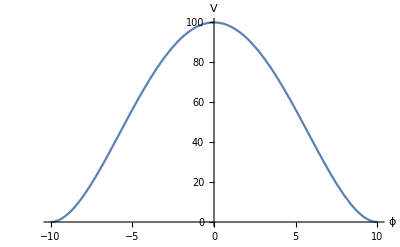

{0.,{x→10.}}

{a,b,c,g} = -1/50, 0, 1/10000, 1.

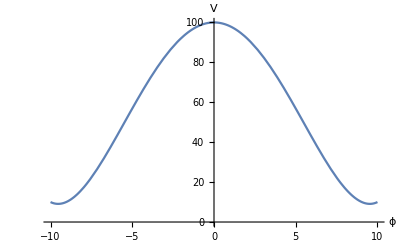

{9.09091,{x→-9.53463}}

{a,b,c,g} = -1/50, 0, 0.00011, 0.909091

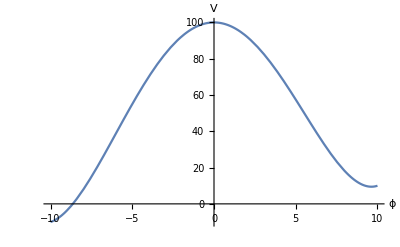

{-10.5841,{x→-10.382}}

{a,b,c,g} = -1/50, 0.0001, 1/10000, 1.10584

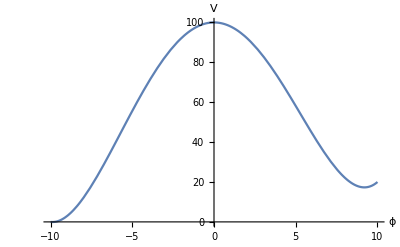

{-0.0588317,{x→-9.88163}}

{a,b,c,g} = -1/50, 0.0001, 0.00011, 1.00059

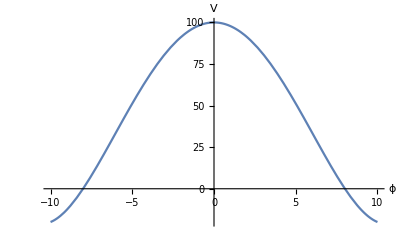

{-21.,{x→10.4881}}

{a,b,c,g} = -0.022, 0, 1/10000, 1.21

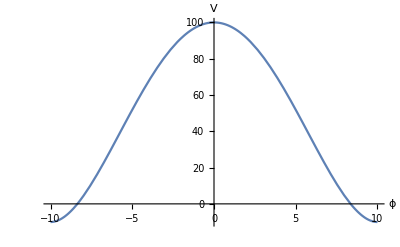

{-10.,{x→10.}}

{a,b,c,g} = -0.022, 0, 0.00011, 1.1

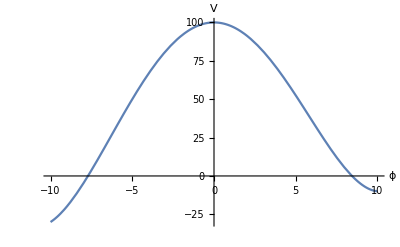

{-33.1783,{x→-10.8698}}

{a,b,c,g} = -0.022, 0.0001, 1/10000, 1.33178

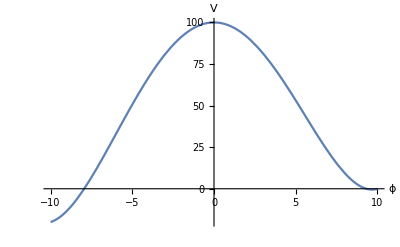

{-20.5292,{x→-10.3467}}

{a,b,c,g} = -0.022, 0.0001, 0.00011, 1.20529

masterList = {}

```mathematica
(* v[x_]:= 1 + a*x^2 + b*x^3 + c*x^4 *)
output = False;
left = True;
σ = 10;
aList = -2/σ^2*{1,1.1,1.2,-0.9,-0.8,1.3,-0.7};
bList = {0,0.0001,0.001,-0.001,0.0001,0.0005,-0.0005};
cList = 1/σ^4*{1,1.1,1.2,-0.9,-0.8,1.3,-0.7};
d = 0.01*σ^4;
masterList = {};masterListAll = {};
Do[ Do[ Do[
v[x_]:=d*(1 + a*x^2 + b*x^3 + c*x^4);
Print[Plot[v[x],{x,-10,10},AxesLabel->{"ϕ","V"}]];
minList = Minimize[v[x],x];
Print[minList];
If[Abs[x/.minList[[2]]]<eps,Continue[]];
If[Abs[x/.minList[[2]]]>100,Continue[]];
g = Check[1-First@minList/d,0];
v[x_]:=d*(g + a*x^2 + b*x^3 + c*x^4);
Print["{a,b,c,g} = ",a,", ",b,", ",c,", ",g];

vp[x_]=v'[x];
vpp[x_] = v''[x];
ni = 80; 
nf = -1.8; 
ni2 = 80;
nf2 = 0;
n1guess = -1;

ϕsol2=findϕsol[v,vp,vpp,ni,nf,ni2,nf2,n1guess,output,output, left];
If[%===$Aborted,Continue[]];
{ns,r,ϵ2} = findNsR[v,vp,ϕsol2,ni2,nf2,output,output];
Z = countZeros[ϵ2,nf2,ni2,1];
Print["{a,b,c,Z} = ",a,", ",b,", ",c,", ",Z];

masterList = Append[masterList,{g,a,b,c,Z}];
masterListAll = Append[masterList,{g,a,b,c,ns,r,ϵ2,Z}];

,{c,cList}]
,{b,bList}]
,{a,aList}]
masterList = Partition[masterList,5];
masterListAll = Partition[masterListAll,8];
Print["masterList = ",MatrixForm[masterList]];
rint["masterListAll = ",MatrixForm[masterListAll]];
```

### Old stuff

```mathematica
{ϵsr,ηsr,ηsrL} = findSRparams[v,vp,vpp,ϕsol2,ni2,nf2,True,True];
Plot[{Legended[Evaluate[ηsr[n]],"ηsr"],Legended[Evaluate[ηsrL[n]],"ηsrL"]},{n,nf2,ni2},AxesLabel->{N,"ηsr"},PlotRange->{{nf2,ni2},{0,3}}]
(* Plots,Prints *)
Print["ns[60] = ",ns/.{n->60}," and r[60] = ",r/.{n->60}];
Print["ns[50] = ",ns/.{n->50}," and r[50] = ",r/.{n->50}];
```

```mathematica
Zη = countAllZeros[v,vpp,ηsr,nf2,ni2,0.1,5];
Print["Zη = ",Zη];
```

```mathematica
Zϵ = findZϵ[ϕsol,nf2,ni2,0.1,5];
Print["Zϵ = ",Zϵ];
```

```mathematica
Zη = findZη[ϕsol,nf2,ni2,0.1,5];
Print["Zη = ",Zη];
```

```mathematica
MaxValue[ϵsr[n],n]
Plot[Evaluate[ϵsr[n]],{n,0,80},AxesLabel->{N,"ϵsr"},PlotRange->{0,2}]
f1[n_]=D[ϵsr[n],{n,1}];
Plot[Evaluate[f1[n]],{n,0,80},AxesLabel->{N,"ϵsr1"},PlotRange->{-1,1}]
f2[n_]=D[ϵsr[n],{n,2}];
MaxValue[f2[n],n]
Plot[Evaluate[f2[n]],{n,0,80},AxesLabel->{N,"ϵsr2"},PlotRange->{-1,1}]
```

```mathematica
Plot[Evaluate[ηsr[n]],{n,0,80},AxesLabel->{N,"ηsr1"}]
f1[n_]=D[ηsr[n],{n,1}];
Plot[Evaluate[f1[n]],{n,0,80},AxesLabel->{N,"ηsr1"}]
f2[n_]=D[ηsr[n],{n,2}];
Plot[Evaluate[f2[n]],{n,0,80},AxesLabel->{N,"ηsr2"}]
```